### Optimal Response to a Passive Strategy

```mathematica
ClearAll["Global`*"]
```

b(t) = t

b(0.5) = 0.5

Solution: {{a[t]→1.625 t-0.625 t^2}}

a(t) = 1.625 t-0.625 t^2

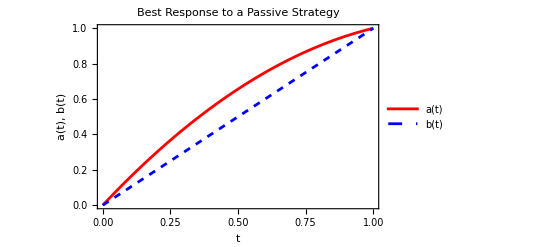

```mathematica
(*Define constants*)λ=5;κ=0.5;σ=3;

(*Define b(t)*)
 b[t_] := t; (* risk-neutral *)

(*Print b(t) to check its definition*)
Print["b(t) = ",b[t]];
Print["b(0.5) = ",b[0.5]];

(*Define the differential equation for a(t)*)
solveForA[]:=Module[{eqns,bcs,sol,aSol},eqns={a''[t]==-(λ/2) (b''[t]+ κ b'[t])};(*b''[t]=0 for b(t)=t*)
bcs={a[0]==0,a[1]==1};
sol=DSolve[{eqns,bcs},a[t],t];
Print["Solution: ",sol];
aSol=a[t]/. sol[[1]];
aSol];

(*Print a(t) to check its definition*)
aSolution=solveForA[];
Print["a(t) = ",aSolution];

(*Plot both a(t) and b(t) with b(t) as a dashed line*)
Plot[{aSolution,b[t]},{t,0,1},PlotLegends->{"a(t)","b(t)"},PlotStyle->{Red,{Blue,Dashed}},Frame->True,FrameLabel->{{"a(t), b(t)","\!\(\*SubscriptBox[\(ξ\), \(a\)]\) = "<>ToString[ξa]<>", σ="<>ToString[σ]},{"t","κ="<>ToString[κ]<>", λ="<>ToString[λ]}},PlotLabel->"Best Response to a Passive Strategy",PlotRange->All]
```

```mathematica
b[t_]
```

t_